# Omicron US analysis: Plotting partitioned case counts

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-us

```mathematica
dataset="omicron-us";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=250;
```

```mathematica
statesToDrop={"New Mexico","Wisconsin","Texas"};
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

PointLegend[colors,{other,Delta,Omicron},LegendMarkerSize→20,LegendLayout→{Row,1},Spacings→{0,1}]

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-10-15","2021-11-01","2021-11-15","2021-12-01","2021-12-15","2022-01-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-10-15

```mathematica
plottingStartDate="2021-11-01";
```

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2022-01-07

```mathematica
states=Union[seqData[[All,2]]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New Mexico,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Texas,Utah,Vermont,Virginia,Washington,Wisconsin}

```mathematica
states=DeleteCases[states,x_/;MemberQ[statesToDrop,x]]
```

{Arizona,California,Colorado,Connecticut,Florida,Georgia,Illinois,Indiana,Louisiana,Maryland,Massachusetts,Michigan,Minnesota,Nebraska,Nevada,New Jersey,New York,North Carolina,North Dakota,Ohio,Oregon,Pennsylvania,Tennessee,Utah,Vermont,Virginia,Washington}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
stateVariantCounts[state_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==state&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
stateSequenceCounts[state_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==state][[All,4]],0]]},{date,dates}]
```

```mathematica
Map[#->stateSequenceCounts[#][[-15;;-1]]&,states]
```

{Arizona→{{2021-12-24,38},{2021-12-25,22},{2021-12-26,94},{2021-12-27,225},{2021-12-28,347},{2021-12-29,120},{2021-12-30,174},{2021-12-31,81},{2022-01-01,57},{2022-01-02,244},{2022-01-03,249},{2022-01-04,289},{2022-01-05,253},{2022-01-06,252},{2022-01-07,165}},California→{{2021-12-24,420},{2021-12-25,82},{2021-12-26,837},{2021-12-27,3180},{2021-12-28,772},{2021-12-29,202},{2021-12-30,652},{2021-12-31,463},{2022-01-01,54},{2022-01-02,884},{2022-01-03,147},{2022-01-04,72},{2022-01-05,38},{2022-01-06,33},{2022-01-07,21}},Colorado→{{2021-12-24,390},{2021-12-25,387},{2021-12-26,267},{2021-12-27,329},{2021-12-28,329},{2021-12-29,618},{2021-12-30,156},{2021-12-31,89},{2022-01-01,18},{2022-01-02,9},{2022-01-03,220},{2022-01-04,18},{2022-01-05,5},{2022-01-06,1},{2022-01-07,2}},Connecticut→{{2021-12-24,135},{2021-12-25,8},{2021-12-26,154},{2021-12-27,252},{2021-12-28,185},{2021-12-29,229},{2021-12-30,291},{2021-12-31,163},{2022-01-01,5},{2022-01-02,97},{2022-01-03,250},{2022-01-04,98},{2022-01-05,41},{2022-01-06,6},{2022-01-07,3}},Florida→{{2021-12-24,13},{2021-12-25,14},{2021-12-26,499},{2021-12-27,327},{2021-12-28,265},{2021-12-29,176},{2021-12-30,158},{2021-12-31,8},{2022-01-01,15},{2022-01-02,111},{2022-01-03,30},{2022-01-04,11},{2022-01-05,25},{2022-01-06,3},{2022-01-07,15}},Georgia→{{2021-12-24,19},{2021-12-25,9},{2021-12-26,225},{2021-12-27,242},{2021-12-28,214},{2021-12-29,135},{2021-12-30,95},{2021-12-31,3},{2022-01-01,0},{2022-01-02,38},{2022-01-03,33},{2022-01-04,13},{2022-01-05,1},{2022-01-06,0},{2022-01-07,0}},Illinois→{{2021-12-24,31},{2021-12-25,15},{2021-12-26,241},{2021-12-27,243},{2021-12-28,150},{2021-12-29,78},{2021-12-30,87},{2021-12-31,32},{2022-01-01,19},{2022-01-02,44},{2022-01-03,49},{2022-01-04,38},{2022-01-05,16},{2022-01-06,14},{2022-01-07,16}},Indiana→{{2021-12-24,0},{2021-12-25,0},{2021-12-26,51},{2021-12-27,114},{2021-12-28,57},{2021-12-29,43},{2021-12-30,9},{2021-12-31,2},{2022-01-01,0},{2022-01-02,21},{2022-01-03,23},{2022-01-04,44},{2022-01-05,14},{2022-01-06,29},{2022-01-07,17}},Louisiana→{{2021-12-24,39},{2021-12-25,3},{2021-12-26,42},{2021-12-27,73},{2021-12-28,223},{2021-12-29,233},{2021-12-30,165},{2021-12-31,35},{2022-01-01,24},{2022-01-02,186},{2022-01-03,43},{2022-01-04,8},{2022-01-05,7},{2022-01-06,20},{2022-01-07,0}},Maryland→{{2021-12-24,68},{2021-12-25,90},{2021-12-26,98},{2021-12-27,109},{2021-12-28,124},{2021-12-29,241},{2021-12-30,69},{2021-12-31,63},{2022-01-01,58},{2022-01-02,77},{2022-01-03,53},{2022-01-04,40},{2022-01-05,46},{2022-01-06,38},{2022-01-07,24}},Massachusetts→{{2021-12-24,28},{2021-12-25,6},{2021-12-26,705},{2021-12-27,1208},{2021-12-28,682},{2021-12-29,1386},{2021-12-30,1214},{2021-12-31,168},{2022-01-01,170},{2022-01-02,942},{2022-01-03,1629},{2022-01-04,1180},{2022-01-05,877},{2022-01-06,826},{2022-01-07,132}},Michigan→{{2021-12-24,8},{2021-12-25,9},{2021-12-26,76},{2021-12-27,161},{2021-12-28,84},{2021-12-29,52},{2021-12-30,40},{2021-12-31,17},{2022-01-01,1},{2022-01-02,23},{2022-01-03,69},{2022-01-04,8},{2022-01-05,0},{2022-01-06,0},{2022-01-07,0}},Minnesota→{{2021-12-24,30},{2021-12-25,31},{2021-12-26,30},{2021-12-27,25},{2021-12-28,94},{2021-12-29,589},{2021-12-30,55},{2021-12-31,34},{2022-01-01,12},{2022-01-02,21},{2022-01-03,55},{2022-01-04,25},{2022-01-05,0},{2022-01-06,0},{2022-01-07,0}},Nebraska→{{2021-12-24,20},{2021-12-25,17},{2021-12-26,42},{2021-12-27,120},{2021-12-28,143},{2021-12-29,103},{2021-12-30,30},{2021-12-31,36},{2022-01-01,37},{2022-01-02,34},{2022-01-03,50},{2022-01-04,59},{2022-01-05,28},{2022-01-06,37},{2022-01-07,32}},Nevada→{{2021-12-24,10},{2021-12-25,8},{2021-12-26,113},{2021-12-27,243},{2021-12-28,26},{2021-12-29,22},{2021-12-30,11},{2021-12-31,25},{2022-01-01,0},{2022-01-02,1},{2022-01-03,6},{2022-01-04,2},{2022-01-05,16},{2022-01-06,5},{2022-01-07,3}},New Jersey→{{2021-12-24,23},{2021-12-25,4},{2021-12-26,95},{2021-12-27,131},{2021-12-28,70},{2021-12-29,212},{2021-12-30,130},{2021-12-31,75},{2022-01-01,4},{2022-01-02,18},{2022-01-03,12},{2022-01-04,29},{2022-01-05,12},{2022-01-06,0},{2022-01-07,1}},New York→{{2021-12-24,209},{2021-12-25,91},{2021-12-26,71},{2021-12-27,358},{2021-12-28,298},{2021-12-29,236},{2021-12-30,89},{2021-12-31,89},{2022-01-01,21},{2022-01-02,39},{2022-01-03,98},{2022-01-04,162},{2022-01-05,97},{2022-01-06,19},{2022-01-07,15}},North Carolina→{{2021-12-24,70},{2021-12-25,36},{2021-12-26,109},{2021-12-27,322},{2021-12-28,206},{2021-12-29,308},{2021-12-30,237},{2021-12-31,52},{2022-01-01,49},{2022-01-02,74},{2022-01-03,184},{2022-01-04,205},{2022-01-05,129},{2022-01-06,42},{2022-01-07,57}},North Dakota→{{2021-12-24,21},{2021-12-25,9},{2021-12-26,20},{2021-12-27,57},{2021-12-28,125},{2021-12-29,35},{2021-12-30,79},{2021-12-31,21},{2022-01-01,4},{2022-01-02,42},{2022-01-03,70},{2022-01-04,40},{2022-01-05,102},{2022-01-06,11},{2022-01-07,21}},Ohio→{{2021-12-24,2},{2021-12-25,1},{2021-12-26,74},{2021-12-27,89},{2021-12-28,36},{2021-12-29,14},{2021-12-30,107},{2021-12-31,0},{2022-01-01,0},{2022-01-02,1},{2022-01-03,96},{2022-01-04,94},{2022-01-05,54},{2022-01-06,0},{2022-01-07,1}},Oregon→{{2021-12-24,33},{2021-12-25,12},{2021-12-26,62},{2021-12-27,92},{2021-12-28,106},{2021-12-29,99},{2021-12-30,69},{2021-12-31,34},{2022-01-01,21},{2022-01-02,20},{2022-01-03,77},{2022-01-04,226},{2022-01-05,183},{2022-01-06,111},{2022-01-07,132}},Pennsylvania→{{2021-12-24,27},{2021-12-25,0},{2021-12-26,49},{2021-12-27,56},{2021-12-28,66},{2021-12-29,146},{2021-12-30,83},{2021-12-31,54},{2022-01-01,0},{2022-01-02,19},{2022-01-03,0},{2022-01-04,0},{2022-01-05,2},{2022-01-06,0},{2022-01-07,1}},Tennessee→{{2021-12-24,14},{2021-12-25,8},{2021-12-26,42},{2021-12-27,198},{2021-12-28,82},{2021-12-29,92},{2021-12-30,141},{2021-12-31,52},{2022-01-01,6},{2022-01-02,0},{2022-01-03,43},{2022-01-04,3},{2022-01-05,0},{2022-01-06,0},{2022-01-07,0}},Utah→{{2021-12-24,15},{2021-12-25,18},{2021-12-26,257},{2021-12-27,321},{2021-12-28,247},{2021-12-29,280},{2021-12-30,261},{2021-12-31,3},{2022-01-01,4},{2022-01-02,37},{2022-01-03,619},{2022-01-04,516},{2022-01-05,176},{2022-01-06,0},{2022-01-07,1}},Vermont→{{2021-12-24,0},{2021-12-25,0},{2021-12-26,37},{2021-12-27,60},{2021-12-28,7},{2021-12-29,28},{2021-12-30,5},{2021-12-31,1},{2022-01-01,0},{2022-01-02,1},{2022-01-03,265},{2022-01-04,30},{2022-01-05,64},{2022-01-06,12},{2022-01-07,134}},Virginia→{{2021-12-24,1},{2021-12-25,1},{2021-12-26,19},{2021-12-27,21},{2021-12-28,31},{2021-12-29,198},{2021-12-30,39},{2021-12-31,0},{2022-01-01,0},{2022-01-02,3},{2022-01-03,1},{2022-01-04,1},{2022-01-05,0},{2022-01-06,0},{2022-01-07,0}},Washington→{{2021-12-24,263},{2021-12-25,7},{2021-12-26,94},{2021-12-27,284},{2021-12-28,430},{2021-12-29,280},{2021-12-30,229},{2021-12-31,139},{2022-01-01,43},{2022-01-02,211},{2022-01-03,106},{2022-01-04,74},{2022-01-05,53},{2022-01-06,4},{2022-01-07,0}}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[state_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==state,{0,0,0}][[3]]},{date,dates}]]
```

## Variant frequencies

### Transforming frequencies to logistic space

```mathematica
daysBackForEstimate=15;
```

```mathematica
daysForwardForProjection=0;
```

```mathematica
clippingThresold=0.0001;
```

```mathematica
logitTransform[x_]:=Log[x/(1-x)]
```

```mathematica
logitBackTransform[y_]:=Exp[y]/(1+ Exp[y])
```

```mathematica
retransformPrevSeries[logisticSeries_]:=Map[{#[[1]],logitBackTransform[#[[2]]]}&,logisticSeries]
```

```mathematica
logisticPrevSeries[positivesSeries_,totalsSeries_]:=Module[{prevSeries,clipped},
prevSeries=smoothedPrevalence[positivesSeries,totalsSeries];
Map[{#[[1]],Which[#[[2]]<0.0001,logitTransform[0.0001],#[[2]]>0.9999,logitTransform[0.9999],True,logitTransform[#[[2]]]]}&,prevSeries]
]
```

```mathematica
modeledLogisticPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],lm[x]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
modeledGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],#[[2]]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>logitTransform[clippingThresold]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{0.82,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

### Plotting functions

```mathematica
logitMinFreq=0.0001;logitMaxFreq=0.995;legendStartingPointY=0.95;
```

```mathematica
maxFreq=1;
```

```mathematica
logitTicks=Map[{logitTransform[#],ToString[If[#<0.01,NumberForm[Round[100*#,0.1],{3,1}],Round[100*#]]]<>"%"}&,{0.001,0.01,0.1,0.5,0.9,0.99}];
```

```mathematica
logisticFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=Module[{clippedPrev,clippedModeled},
clippedPrev=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,prev];
clippedModeled=Map[Cases[#,x_/;x[[2]]>logitTransform[logitMinFreq]]&,modeled];
DateListPlot[Join[clippedPrev,clippedModeled],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{logitTicks,Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{logitTransform[logitMinFreq],logitTransform[If[maxFreq>logitMaxFreq,logitMaxFreq,maxFreq]]}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
]
```

```mathematica
naturalFreqPlotMultipleLineages[prev_,modeled_,legend_,country_]:=DateListPlot[Map[retransformPrevSeries,Join[prev,modeled]],Frame->{True,True,False,False},FrameLabel->{"Specimen collection date","Variant frequency"},PlotTheme->"FullAxes",FrameTicks->{{Map[{#,ToString[Round[100*#]]<>"%"}&,Range[0,1,If[maxFreq>0.5,0.2,0.1]]],Automatic},{dateTicks,Automatic}},PlotStyle->Append[colors,colors[[3]]],PlotRange->{{plottingStartDate,endDate},{0,maxFreq}},ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{48,12},{35,5}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},Joined->Join[Table[False,{n}],Table[True,{n}]],PlotMarkers->Join[Table[{"•",Tiny},{n}],Table[None,{n}]],PlotRangeClipping->True,Epilog->{Style[{Black,Text[country,Scaled[{0.02,legendStartingPointY}],{-1,0}]},FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],legend}]
```

```mathematica
freqForCountry[state_]:=Map[logisticPrevSeries[stateVariantCounts[state,#],stateSequenceCounts[state]]&,variants]
```

### Panels for each country, each with multiple lineages

```mathematica
freqsForStates=Map[freqForCountry,states];
```

```mathematica
modeledFreqsForStates=Map[{modeledLogisticPrevSeries[logisticPrevSeries[stateVariantCounts[#,"Omicron"],stateSequenceCounts[#]]]}&,states];
```

```mathematica
legendsForStates=Map[constructGrowthRateLegend[modeledGrowthRate[#[[3]]],variants[[3]],legendStartingPointY- 0.09,colors[[3]]]&,freqsForStates];
```

```mathematica
panels=MapThread[logisticFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figLogistic=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-transformed-axis.png",figLogistic,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-transformed-axis.png

```mathematica
panels=MapThread[naturalFreqPlotMultipleLineages,{freqsForStates,modeledFreqsForStates,legendsForStates,states}];
```

```mathematica
figNatural=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_logistic-growth-natural-axis.png",figNatural,"PNG",ImageResolution->300]
```

figures/omicron-us_logistic-growth-natural-axis.png

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[state_,variant_]:=Module[{stateVariantFrequencyDateSeries,stateCasesDateSeries,tuples},
stateVariantFrequencyDateSeries=smoothedPrevalence[stateVariantCounts[state,variant],stateSequenceCounts[state]];
stateCasesDateSeries=csGather[state];
tuples=compareWithDate[stateVariantFrequencyDateSeries,stateCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

### Stacked streamplot

```mathematica
splitCasePlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
StackedDateListPlot[Reverse[variantSeries],Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{0,All}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,Reverse[colors]],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

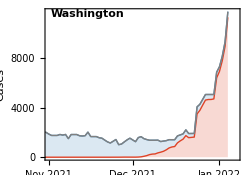

```mathematica
splitCasePlot["Washington"]
```

```mathematica
panels=Map[splitCasePlot,states];
```

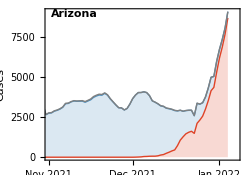
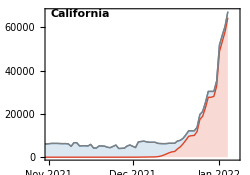
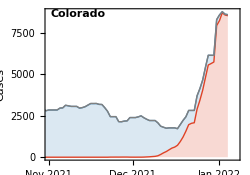
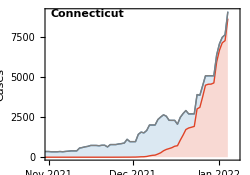
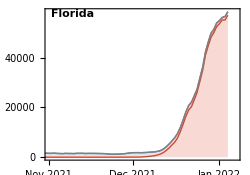
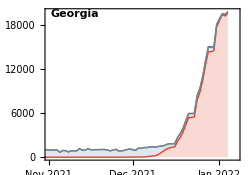
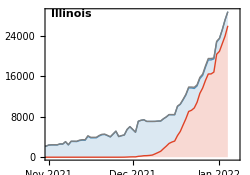
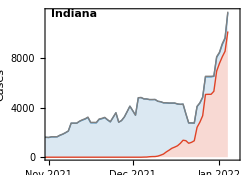
|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-cases.png

### Log cases line plot with growth rate

```mathematica
maxY=50000;
```

```mathematica
splitCaseLogPlot[state_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
splitCaseLogPlot[state_,legend_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[state,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->False,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->{Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],legend}]
]
```

```mathematica
modeledExpPrevSeries[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
Table[{DateString[DatePlus[dateMin,x],{"Year","-","Month", "-","Day"}],Exp[lm[x]]},{x,diff-daysBackForEstimate,diff+daysForwardForProjection}]
]
```

```mathematica
splitCaseLogPlotModeledOmicron[state_]:=Module[{variantSeries,modeledVariantSeries},
variantSeries=csVariantGather[state,"Omicron"];
modeledVariantSeries=modeledExpPrevSeries[variantSeries];
DateListLogPlot[modeledVariantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.7,ImagePadding->{{55,15},{15,10}},Joined->True,PlotRange->{{plottingStartDate,endDate},
{20,maxY}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotStyle->colors[[3]],FrameTicks->{{{10,100,1000,10000,100000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[state,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
modeledExpGrowthRate[prevSeries_]:=Module[{dateMin,dateMax,diff,prevPairs,trimmed,clipped,lm,best,lower,upper},
dateMin=prevSeries[[1,1]];
dateMax=prevSeries[[-1,1]];
diff=QuantityMagnitude[DateDifference[dateMin,dateMax]];
prevPairs=Map[{QuantityMagnitude[DateDifference[dateMin,#[[1]]]],Log[#[[2]]+0.1]}&,prevSeries];
trimmed=prevPairs[[-daysBackForEstimate;;-1]];
clipped=Cases[trimmed,x_/;x[[2]]>Log[1]];
lm=LinearModelFit[clipped,{1,x},x];
best=lm["BestFitParameters"][[2]];
lower=lm["ParameterConfidenceIntervals"][[2,1]];
upper=lm["ParameterConfidenceIntervals"][[2,2]];
{best,lower,upper}
]
```

```mathematica
constructExpGrowthRateLegend[values_,label_,y_,col_]:=Module[{best,lower,upper},
best=values[[1]];
lower=values[[2]];
upper=values[[3]];
{White,Rectangle[Scaled[{0.01,y-0.05}],Scaled[{1,y+0.05}]],Style[{col,PointSize[0.03],Point[Scaled[{0.04,y+0.01}]],Black,Text["r = "<>ToString[NumberForm[Round[best,0.01],{3,2}]]<>" per day ("<>ToString[NumberForm[Round[lower,0.01],{3,2}]]<>", "<>ToString[NumberForm[Round[upper,0.01],{3,2}]]<>")",Scaled[{0.075,y}],{-1,0},Background->White]},FontSize->11,FontFamily->"Helvetica"]}
]
```

```mathematica
legendsForStates=Map[constructExpGrowthRateLegend[modeledExpGrowthRate[csVariantGather[#,"Omicron"]],"Omicron",legendStartingPointY- 0.09,colors[[3]]]&,states];
```

```mathematica
panels=MapThread[Show[splitCaseLogPlot[#1,#2],splitCaseLogPlotModeledOmicron[#1]]&,{states,legendsForStates}];
```

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft,SpanFromLeft},panels],4],Spacings->{0,0},Alignment->Right]
```

|  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-us_partitioned-log-cases.png